```mathematica
(*
  stri1 and stri2 are the two solutions

    (s2 +/- Sqrt[s2 (s2 - 4 m^2)])/(2 m^2).

  Initially these two triangle branch points are on the triangle
  second sheet.  As s2 is continued from M^2 + i epsilon to the
  unstable pole M^2 - i M Gamma, they enter the triangle first sheet.

  The sheet of the s2 square root and the sheet occupied by a triangle
  branch point are different notions.  The stri functions label the
  two algebraic branch-point solutions, not Riemann sheets.
*)
ClearAll[
  triangleRootUpperRim, triangleRootAfterCut,
  triangleRootOnPath, stri1, stri2,
  stri1OnPath, stri2OnPath
];

(* Physical-cut convention:
   q[x + i 0] = +Sqrt[x (x - 4 m^2)] for x > 4 m^2. *)
triangleRootUpperRim[si_, m_] := I Sqrt[si] Sqrt[4 m^2 - si];

(* Analytic continuation of the same root through the cut. *)
triangleRootAfterCut[si_, m_] := -triangleRootUpperRim[si, m];

(* Algebraic locations of the two triangle branch points, evaluated
   with the upper-rim root convention.  Their triangle-sheet labels
   are assigned separately along the continuation path below. *)
stri1[si_, m_] :=
  (si + triangleRootUpperRim[si, m])/(2 m^2);

stri2[si_, m_] :=
  (si - triangleRootUpperRim[si, m])/(2 m^2);
```

triangle-root sheet-matching error = 0.+0.0000358456 ⅈ

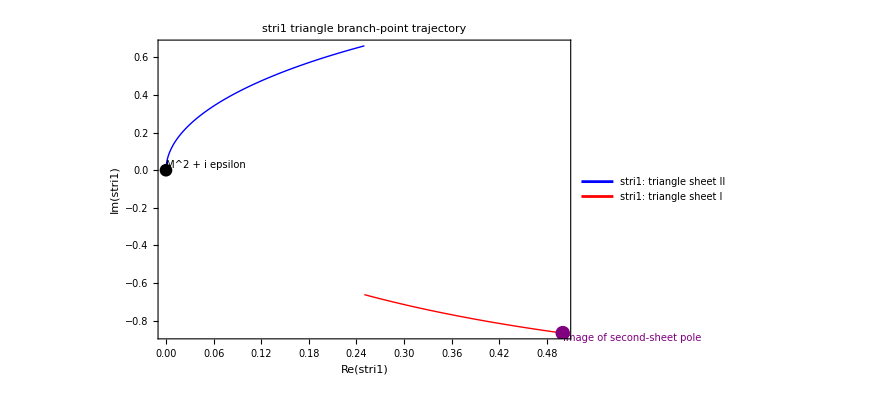

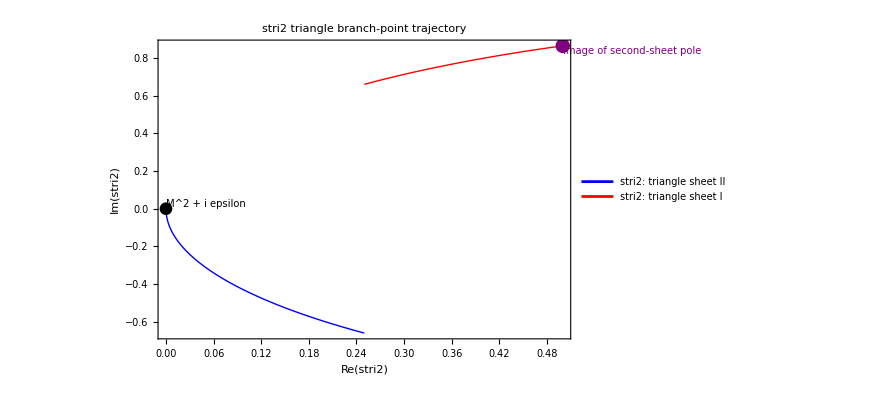

```mathematica
m0 = 1.;
resonanceM = 2.10;
resonanceWidth = 0.10;

(* Same convention as M^2 - i M Gamma in unsB2. *)
sPole = resonanceM^2 - I resonanceM resonanceWidth;
threshold = 4 m0^2;
iEpsilon = 10^-5 m0^2;

(* Continue the unstable invariant from the upper rim to its pole.
   t = 0: s2 = M^2 + i epsilon.
   t = 1/2: cross the s2 decay cut at M^2.
   t = 1: s2 = M^2 - i M Gamma. *)
s2Start = resonanceM^2 + I iEpsilon;

ClearAll[s2Path, complexCoordinates];

s2Path[t_?NumericQ] := Piecewise[{
  {
    t + I 0,
    0 <= t <= threshold
  },
  {
    resonanceM^2 + I iEpsilon (1 - 2 t),
    0 <= t <= 1/2
  },
  {
    resonanceM^2 - I resonanceM resonanceWidth (2 t - 1),
    1/2 < t <= 1
  }
}];

(* Continue one common square root. Switching its sign at the cut
   keeps both algebraic triangle branch-point trajectories continuous.
   The triangle points themselves go from triangle sheet II to I. *)
triangleRootOnPath[t_?NumericQ] := If[
  t <= 1/2,
  triangleRootUpperRim[s2Path[t], m0],
  triangleRootAfterCut[s2Path[t], m0]
];

stri1OnPath[t_?NumericQ] :=
  (s2Path[t] + triangleRootOnPath[t])/(2 m0^2);

stri2OnPath[t_?NumericQ] :=
  (s2Path[t] - triangleRootOnPath[t])/(2 m0^2);

complexCoordinates[z_?NumericQ] := N[{Re[z], Im[z]}];

(* This must approach zero as iEpsilon -> 0. *)
rootMatchingError = N[
  triangleRootUpperRim[resonanceM^2 + I iEpsilon, m0] -
   triangleRootAfterCut[resonanceM^2 - I iEpsilon, m0]
];
Print["triangle-root sheet-matching error = ", rootMatchingError];

(* Do not sample exactly on the projected cut, where a sheet label is
   ambiguous. *)
sheetGap = 10^-5;
triangleSheetIITimes = Subdivide[0., 1/2 - sheetGap, 350];
triangleSheetITimes = Subdivide[1/2 + sheetGap, 1., 350];

stri1TriangleSheetIIData =
  complexCoordinates[stri1OnPath[#]] & /@ triangleSheetIITimes;
stri1TriangleSheetIData =
  complexCoordinates[stri1OnPath[#]] & /@ triangleSheetITimes;

stri2TriangleSheetIIData =
  complexCoordinates[stri2OnPath[#]] & /@ triangleSheetIITimes;
stri2TriangleSheetIData =
  complexCoordinates[stri2OnPath[#]] & /@ triangleSheetITimes;

cutRoot = Sqrt[resonanceM^2 (resonanceM^2 - threshold)];
stri1CutImage = {
  (resonanceM^2 + cutRoot)/(2 m0^2),
  0.
};
stri2CutImage = {
  (resonanceM^2 - cutRoot)/(2 m0^2),
  0.
};
stri1PoleImage = complexCoordinates[stri1OnPath[1.]];
stri2PoleImage = complexCoordinates[stri2OnPath[1.]];

ClearAll[makeTriangleTrajectoryPlot];

makeTriangleTrajectoryPlot[
   sheetIIData_, sheetIData_, branchName_String, cutImage_,
   poleImage_] :=
 ListLinePlot[
  {sheetIIData, sheetIData},
  PlotStyle -> {
    Directive[Blue, Thick],
    Directive[Red, Thick]
  },
  PlotLegends -> {
    branchName <> ": triangle sheet II",
    branchName <> ": triangle sheet I"
  },
  Frame -> True,
  Axes -> False,
  FrameLabel -> {
    "Re(" <> branchName <> ")",
    "Im(" <> branchName <> ")"
  },
  PlotLabel -> branchName <> " triangle branch-point trajectory",
  PlotRange -> All,
  Epilog -> {
    Black, PointSize[0.014], Point[First[sheetIIData]],
    Text[
      Style["M^2 + i epsilon", 10, Black],
      First[sheetIIData],
      {-1, -1}
    ],

    Darker[Green], PointSize[0.016], Point[cutImage],
    Text[
      Style["cross s2 cut", 10, Darker[Green]],
      cutImage,
      {-1, 1}
    ],

    Purple, PointSize[0.016], Point[poleImage],
    Text[
      Style["image of second-sheet pole", 10, Purple],
      poleImage,
      {-1, 1}
    ]
  },
  ImageSize -> 650
];

stri1TrajectoryPlot = makeTriangleTrajectoryPlot[
  stri1TriangleSheetIIData,
  stri1TriangleSheetIData,
  "stri1",
  stri1CutImage,
  stri1PoleImage
];

stri2TrajectoryPlot = makeTriangleTrajectoryPlot[
  stri2TriangleSheetIIData,
  stri2TriangleSheetIData,
  "stri2",
  stri2CutImage,
  stri2PoleImage
];

(* Display the two trajectories as two separate plots. *)
Print[stri1TrajectoryPlot];
Print[stri2TrajectoryPlot];
```

```mathematica
(*
  stri1 and stri2 are the two solutions

    (s2 +/- Sqrt[s2 (s2 - 4 m^2)])/(2 m^2).

  Initially these two triangle branch points are on the triangle
  second sheet.  As s2 is continued from M^2 + i epsilon to the
  unstable pole M^2 - i M Gamma, they enter the triangle first sheet.

  The sheet of the s2 square root and the sheet occupied by a triangle
  branch point are different notions.  The stri functions label the
  two algebraic branch-point solutions, not Riemann sheets.
*)
ClearAll[
  triangleRootUpperRim, triangleRootAfterCut,
  triangleRootOnPath, stri1, stri2,
  stri1OnPath, stri2OnPath
];

(* Physical-cut convention:
   q[x + i 0] = +Sqrt[x (x - 4 m^2)] for x > 4 m^2. *)
triangleRootUpperRim[si_, m_] := I Sqrt[si] Sqrt[4 m^2 - si];

(* Analytic continuation of the same root through the cut. *)
triangleRootAfterCut[si_, m_] := -triangleRootUpperRim[si, m];

(* Algebraic locations of the two triangle branch points, evaluated
   with the upper-rim root convention.  Their triangle-sheet labels
   are assigned separately along the continuation path below. *)
stri1[si_, m_] :=
  (si + triangleRootUpperRim[si, m])/(2 m^2);

stri2[si_, m_] :=
  (si - triangleRootUpperRim[si, m])/(2 m^2);
```

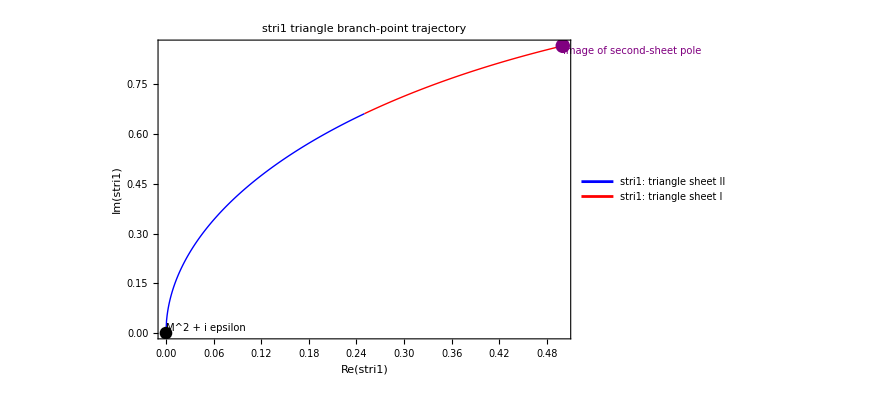

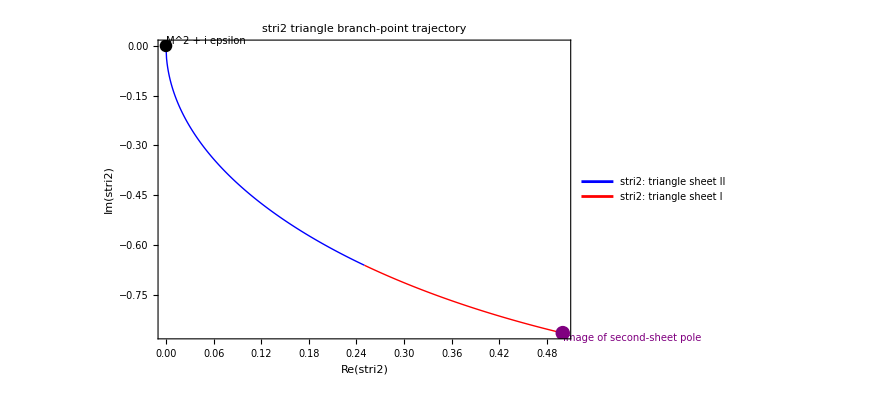

```mathematica
m0 = 1.;
resonanceM = 2.10;
resonanceWidth = 0.10;

(* Same convention as M^2 - i M Gamma in unsB2. *)
sPole = resonanceM^2 - I resonanceM resonanceWidth;
threshold = 4 m0^2;
iEpsilon = 10^-5 m0^2;

(* Continue the unstable invariant from the upper rim to its pole.
   t = 0: s2 = M^2 + i epsilon.
   t = 1/2: cross the s2 decay cut at M^2.
   t = 1: s2 = M^2 - i M Gamma. *)
s2Start = resonanceM^2 - I iEpsilon;

ClearAll[s2Path, complexCoordinates];

s2Path[t_?NumericQ] := Piecewise[{
  {
    t + I 0,
    0 <= t <= threshold
  },
  {
    resonanceM^2 - I iEpsilon (1 - 2 t),
    0 <= t <= 1/2
  },
  {
    resonanceM^2 - I resonanceM resonanceWidth (2 t - 1),
    1/2 < t <= 1
  }
}];

(* Continue one common square root. Switching its sign at the cut
   keeps both algebraic triangle branch-point trajectories continuous.
   The triangle points themselves go from triangle sheet II to I. *)
triangleRootOnPath[t_?NumericQ] := If[
  t <= 1/2,
  triangleRootUpperRim[s2Path[t], m0],
  triangleRootUpperRim[s2Path[t], m0]
];

stri1OnPath[t_?NumericQ] :=
  (s2Path[t] + triangleRootOnPath[t])/(2 m0^2);

stri2OnPath[t_?NumericQ] :=
  (s2Path[t] - triangleRootOnPath[t])/(2 m0^2);

complexCoordinates[z_?NumericQ] := N[{Re[z], Im[z]}];

(* Do not sample exactly on the projected cut, where a sheet label is
   ambiguous. *)
sheetGap = 10^-5;
triangleSheetIITimes = Subdivide[0., 1/2 - sheetGap, 350];
triangleSheetITimes = Subdivide[1/2 + sheetGap, 1., 350];

stri1TriangleSheetIIData =
  complexCoordinates[stri1OnPath[#]] & /@ triangleSheetIITimes;
stri1TriangleSheetIData =
  complexCoordinates[stri1OnPath[#]] & /@ triangleSheetITimes;

stri2TriangleSheetIIData =
  complexCoordinates[stri2OnPath[#]] & /@ triangleSheetIITimes;
stri2TriangleSheetIData =
  complexCoordinates[stri2OnPath[#]] & /@ triangleSheetITimes;

cutRoot = Sqrt[resonanceM^2 (resonanceM^2 - threshold)];
stri1CutImage = {
  (resonanceM^2 + cutRoot)/(2 m0^2),
  0.
};
stri2CutImage = {
  (resonanceM^2 - cutRoot)/(2 m0^2),
  0.
};
stri1PoleImage = complexCoordinates[stri1OnPath[1.]];
stri2PoleImage = complexCoordinates[stri2OnPath[1.]];

ClearAll[makeTriangleTrajectoryPlot];

makeTriangleTrajectoryPlot[
   sheetIIData_, sheetIData_, branchName_String, cutImage_,
   poleImage_] :=
 ListLinePlot[
  {sheetIIData, sheetIData},
  PlotStyle -> {
    Directive[Blue, Thick],
    Directive[Red, Thick]
  },
  PlotLegends -> {
    branchName <> ": triangle sheet II",
    branchName <> ": triangle sheet I"
  },
  Frame -> True,
  Axes -> False,
  FrameLabel -> {
    "Re(" <> branchName <> ")",
    "Im(" <> branchName <> ")"
  },
  PlotLabel -> branchName <> " triangle branch-point trajectory",
  PlotRange -> All,
  Epilog -> {
    Black, PointSize[0.014], Point[First[sheetIIData]],
    Text[
      Style["M^2 + i epsilon", 10, Black],
      First[sheetIIData],
      {-1, -1}
    ],

    Darker[Green], PointSize[0.016], Point[cutImage],
    Text[
      Style["cross s2 cut", 10, Darker[Green]],
      cutImage,
      {-1, 1}
    ],

    Purple, PointSize[0.016], Point[poleImage],
    Text[
      Style["image of second-sheet pole", 10, Purple],
      poleImage,
      {-1, 1}
    ]
  },
  ImageSize -> 650
];

stri1TrajectoryPlot = makeTriangleTrajectoryPlot[
  stri1TriangleSheetIIData,
  stri1TriangleSheetIData,
  "stri1",
  stri1CutImage,
  stri1PoleImage
];

stri2TrajectoryPlot = makeTriangleTrajectoryPlot[
  stri2TriangleSheetIIData,
  stri2TriangleSheetIData,
  "stri2",
  stri2CutImage,
  stri2PoleImage
];

(* Display the two trajectories as two separate plots. *)
Print[stri1TrajectoryPlot];
Print[stri2TrajectoryPlot];
```